```mathematica
Dynamical Systems TIF155/FIM770
Konstantinos Zakkas
Problem Set 3
```

```mathematica
3.2 Stability exponents for a toy model
```

```mathematica
a)
```

```mathematica
rDot[μ_, r_]=μ*r-r^3
thetaDot[ω_, ν_, r_]=ω+ν*r^2
```

-r^3+r μ

r^2 ν+ω

```mathematica
sols = Solve[rDot[μ,r]==0,r]
```

{{r→0},{r→-√μ},{r→√μ}}

```mathematica
r0=r/.sols[[3]]
```

√μ

```mathematica
The angle after one period is 2π, so we can find the period by solving θ(T)- θ(0)=2 π
```

```mathematica
thetaFunction[t_]=(theta[t]/.DSolve[theta'[t]== thetaDot[ω,ν,r0], theta[t],t][[1]])
```

t μ ν+t ω+C[1]

```mathematica
The period time can then be computed by solving θ(T)-θ(0)=2π:
```

```mathematica
period=t/.Solve[thetaFunction[t]-thetaFunction[0]==2π,t]
```

{(2 π)/(μ ν+ω)}

```mathematica
b)
```

```mathematica
The dynamical system(1) transformed into Cartesian coordinates will be
```

```mathematica
xDot[x_,y_,μ_,ω_,ν_]=μ*x-x^3+-x*y^2-yω-yνx^2+-νy^3
yDot[x_,y_,μ_,ω_,ν_]=μ*y-yx^2+y^3+xω+νx^3+νxy^2
```

-x^3-x y^2-yνx^2-yω+x μ-νy^3

xω+y^3-yx^2+y μ+νx^3+νxy^2

```mathematica
X1Dot = 1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2Dot = X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;

dynSys2 = {X1'[t]== 1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t] == X1[t]+1/10*X2[t]+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
```

```mathematica
Tmax = 100;
sols=NDSolve[Join[dynSys2,Thread[{X1[0],X2[0]}== {1/Sqrt[10], 0}]],{X1[t],X2[t]},{t,0,Tmax}];
```

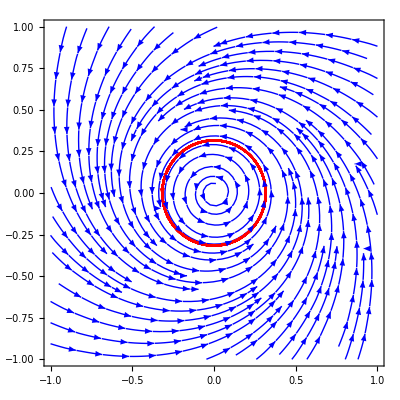

```mathematica
Show[StreamPlot[{X1Dot,X2Dot},{X1,-1,1},{X2,-1,1},StreamStyle->Blue, StreamColorFunction->None],ParametricPlot[Evaluate[{X1[t],X2[t]}/.sols],{t,0,Tmax},PlotStyle->Red]]/.Line[x_]->{Arrowheads[{{0.05,0.1},{0.05,0.4},{0.05,0.6},{0.05,0.7}}],Arrow[x]}
```

```mathematica
c)By comparing the coefficients it is clear that the two systems are identical for μ=1/10, ω=1, ν=1
```

```mathematica
d)
```

```mathematica
μ=1/10;
ω = 1;
ν = 1;
X1Dot[X1_,X2_]=xDot[X1,X2,μ,ω,ν]
X2Dot[X1_,X2_]=yDot[X1,X2,μ,ω,ν];
Tmax = 2π;
```

```mathematica
mat = D[{dynSys2[[1]][[2]],dynSys2[[2]][[2]]},{{X1[t],X2[t]}}]//MatrixForm
```

```mathematica
sols2 = NDSolve[Join[]{dynSys2[[1]],dynSys2[[2]]},M11'[t] == mat[[1]][[1]]*M11[t]+mat[[1]][[2]]*M21[t], M12'[t] == mat[[1]][[1]]*M12[t]+mat[[1]][[2]]*M22[t], M21'[t] == mat[[2]][[1]]*M11[t]+mat[[2]][[2]]*M21[t], M22'[t]== mat[[2]][[1]]*M12[t]+mat[[2]][[2]]*M22[t],X1[0] == Sqrt[μ], X2[0]== 0, M11[0] == 1, M12[0]== 0, M21[0]==0,M22[0]==1}],{X1[t],X2[t], M11[t],M12[t],M21[t],M22[t]},{t,0,Tmax}]]
```